# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];

Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[Total[N[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];
Clear[sur];
sur[eigenval_,eigenvec_,ini_,t_]:=Module[{psit,phases=arrayt[t,eigenval,eigenvec],ck=Conjugate[eigenvec].ini},
Abs[Conjugate[Total[N[ck*phases]]].ini]^2
];
Clear[ExpandBlockVector];
ExpandBlockVector[v_,map_,type_,L_]:=Module[{full=ConstantArray[0,2^L],k=1,a,b,coeff},
Do[
If[Length[pair]==1,full[[pair[[1]]+1]]=v[[k]],{a,b}=pair;
coeff=v[[k]]/Sqrt[2];
If[type=="even",full[[a+1]]=coeff;full[[b+1]]=coeff,full[[a+1]]=coeff;full[[b+1]]=-coeff];];
k++,{pair,map}];
full];
Clear[revIndex];
revIndex[i_,L_]:=FromDigits[Reverse[IntegerDigits[i,2,L]],2];
```

# Symmetries OBC

```mathematica
J=1;
g=1;
h=1;
```

```mathematica
L=4;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[h,0,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
parity=Pauli[{1,1,1,1}];
```

# Survival

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,6,0.00070}];
tlist//Length
```

10001

```mathematica
hlist=Table[(7Sqrt[5])^i,{i,-4,0,0.25}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist=hlist[[1;;-1;;2]]
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

{0.,0.000033137,0.000131101,0.000518677,0.00205205,0.00811857,0.0321197,0.127076,0.502753}

9

```mathematica
L=11;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
allvalues={};
allvectors={};

Do[

Ha=IsingHamiltonian[1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],50];
```

```mathematica
h=-6;
```

```mathematica
phases=ParallelTable[Exp[-I*allvalues[[h]]*t],{t,tlist}];
```

```mathematica
(*Compile only the numeric inner loop*)
Clear[csur];
csur=Compile[{{phases,_Complex,1},{ck,_Complex,1}},Abs[Total[(Abs[ck]^2)*phases]]^2,CompilationTarget->"WVM"];
```

```mathematica
time={};
Do[
ck=Conjugate[allvectors[[h]]].j;
test=ParallelMap[csur[#,ck]&,phases];
AppendTo[time,test]
,{j,productstatesfull}];
```

```mathematica
(*Compile only the numeric inner loop*)
Clear[cipr];
cipr=Compile[{{eigenvec,_Complex,2},{ck,_Complex,1}},Total[(Abs[Conjugate[eigenvec].ck]^4)],CompilationTarget->"WVM"];
```

```mathematica
ipr=ParallelMap[cipr[allvectors[[h]],#]&,productstatesfull];
```

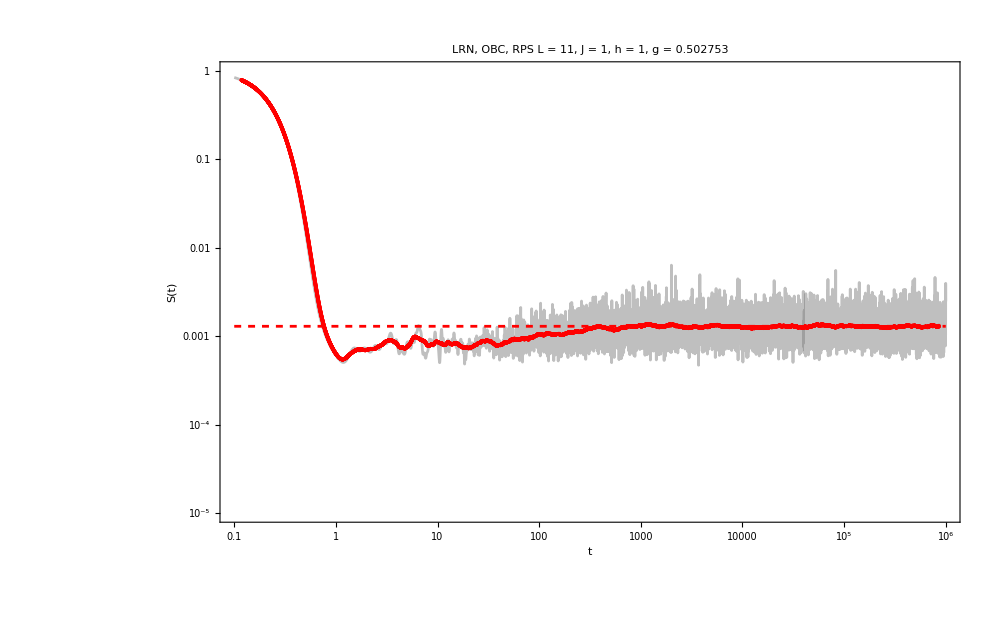

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

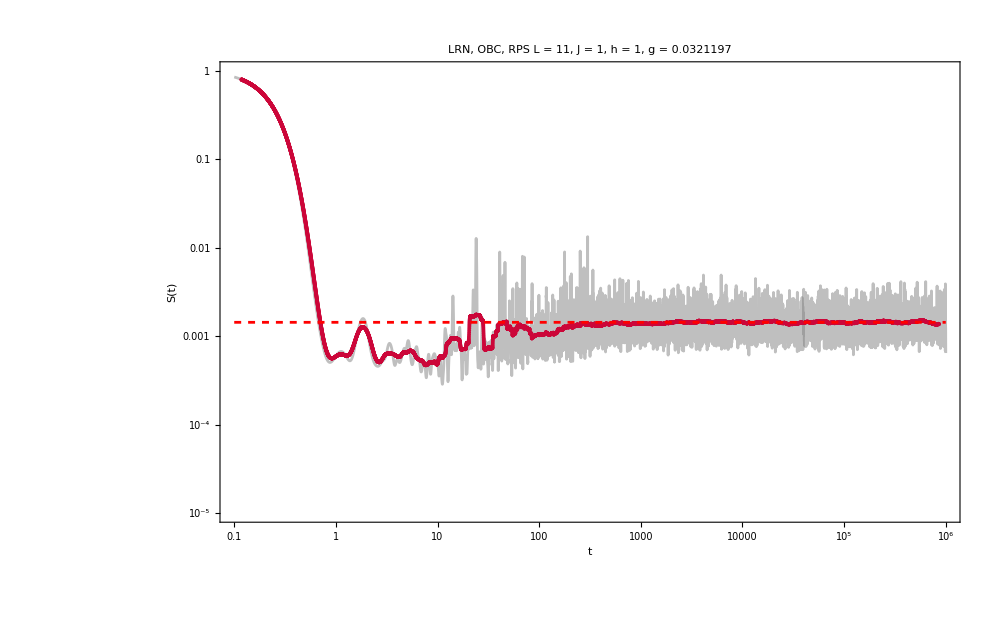

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

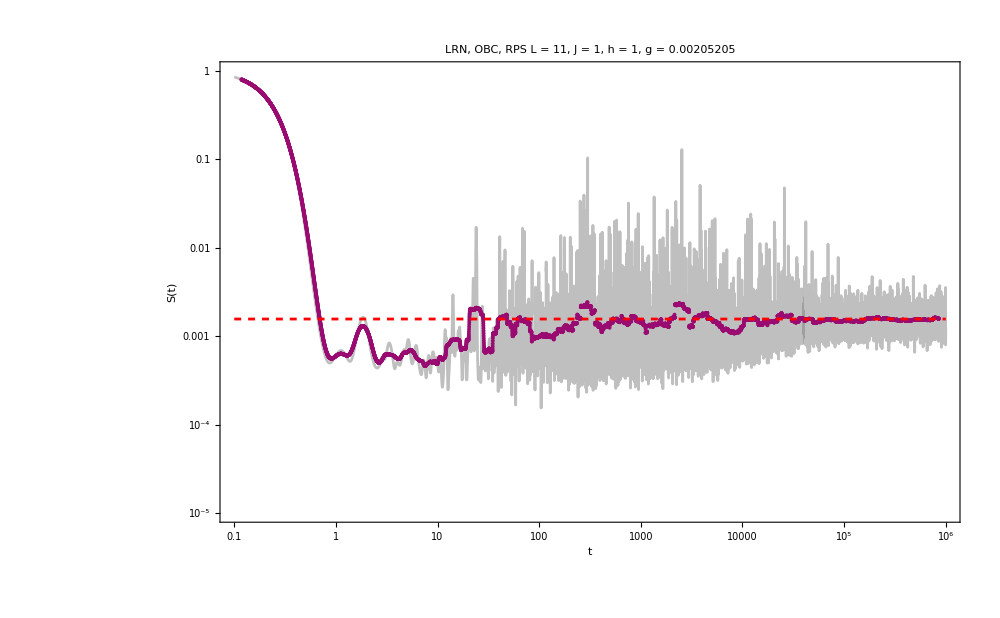

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

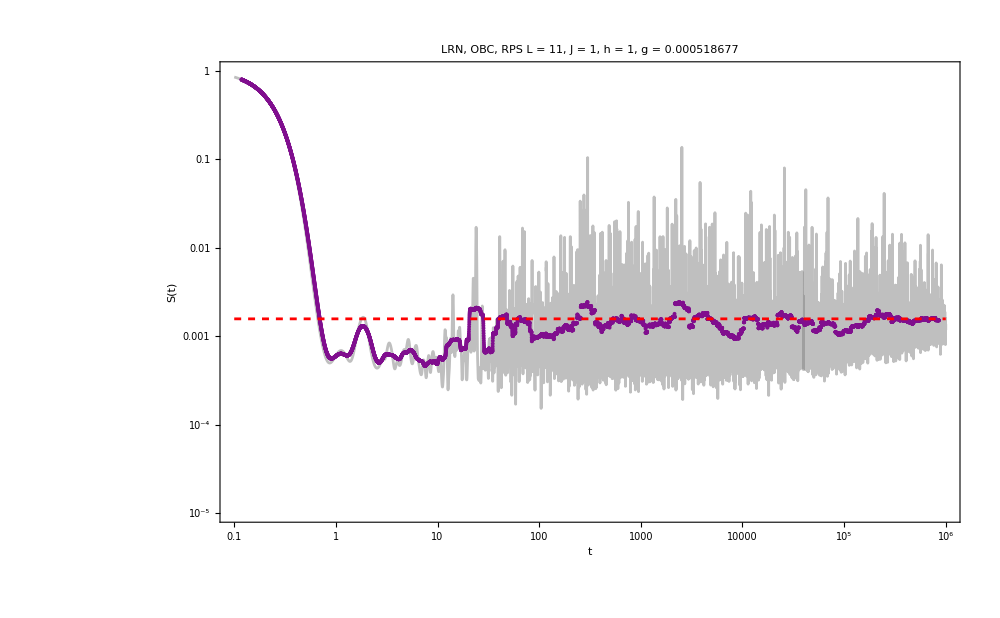

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

# Svn

## test

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,8,0.0010}];
tlist//Length
```

9001

```mathematica
(*hlist=Table[(7Sqrt[5])^i,{i,-4,0,0.1}];*)
(*hlist=hlist[[1;;-1;;2]]*)
hlist=Table[10^i,{i,-6,0,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

32

```mathematica
L=8;
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]/Log[2^(L/2)]];
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
allvalues={};
allvectors={};

Do[

Ha=IsingHamiltonian[1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],50];
```

```mathematica
data={};
Do[

phaseTable=Exp[-I Outer[Times,allvalues[[h]],tlist]];
psitb=Compile[{{ck,_Complex,1},{phaseTable,_Complex,2}},ck*phaseTable,CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];

entropy={};
Do[
ck=Conjugate[allvectors[[h]]].j;
Developer`ToPackedArray/@{allvalues[[h]],allvectors[[h]],ck,phaseTable};
t=psitb[ck,phaseTable];
(*Developer`ToPackedArray[t]; *)
final=Transpose[allvectors[[h]]].t;
(*Developer`ToPackedArray[final];*)
test=ParallelMap[new,Transpose[final]];
AppendTo[entropy,test];
,{j,productstatesfull}];

AppendTo[data,entropy];

,{h,Length[hlist]}];
Export["LRN_OBC_L_"<>ToString[L]<>"_50_RPS.m",data];
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.50]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,Length[hlist]}]
```

```mathematica
Show[plots]
```

## Cycle

```mathematica
Do[

Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]/Log[2^(L/2)]];
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];

allvalues={};
allvectors={};

Do[

Ha=IsingHamiltonian[1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];

productstatesfull=Table[RandomChainProductState[L],50];

data={};
Do[

phaseTable=Exp[-I Outer[Times,allvalues[[h]],tlist]];
psitb=Compile[{{ck,_Complex,1},{phaseTable,_Complex,2}},ck*phaseTable,CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}];

entropy={};
Do[
ck=Conjugate[allvectors[[h]]].j;
Developer`ToPackedArray/@{allvalues[[h]],allvectors[[h]],ck,phaseTable};
t=psitb[ck,phaseTable];
final=Transpose[allvectors[[h]]].t;
test=ParallelMap[new,Transpose[final]];
AppendTo[entropy,test];
,{j,productstatesfull}];

AppendTo[data,entropy];

,{h,Length[hlist]}];
Export["LRN_OBC_L_"<>ToString[L]<>"_50_RPS.m",data];

,{L,{6,8,10,12,14}}];
```

## Example plot LRN

```mathematica
L=6;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\LRN_OBC_L_"<>ToString[L]<>"_50_RPS.m"];
```

```mathematica
limitzero=Mean[data[[1]]][[-1000;;-1]]//Mean;
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]/Log[2^(L/2)]];
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.35]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},GridLines->None,PlotRange->{All,{0,1}}],LogLinearPlot[{pageEntropy[L/2,L/2]/Log[2^(L/2)],limitzero,limitone},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed]},PlotRange->{All,{0,1}}]},Epilog->{Text[Style["g = 0",20,Blue,Bold],Scaled[{0.95,limitzero}],{36.5,1.8}],Text[Style["g = 0.63",20,Red,Bold],Scaled[{0.95,limitone}],{22.5,3}]
},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,{1,-2}}];
(*plot=Show[plots,PlotRange->{All,{0,1}},PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]*)
```

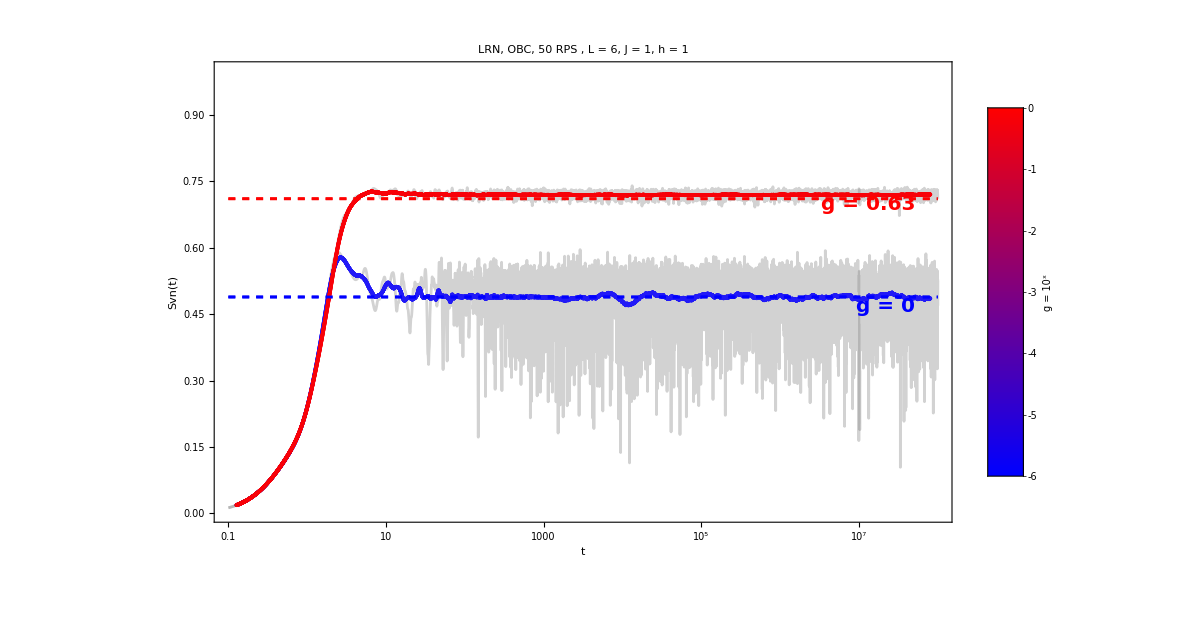

```mathematica
bar=BarLegend[{cf,{-6,0}},LegendLabel->Style["g = \!\(\*SuperscriptBox[\(10\), \(x\)]\)",20,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400}   (*thicker=18,longer=260 px;tweak*)];
finalPlot=Legended[Show[plots,PlotRange->{All,{0,1}}],Placed[bar,Right]]
```

```mathematica
Export["L_"<>ToString[L]<>"_LRNentropy.png",plot]
```

## Example plot all LRN

```mathematica
value=0.6;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.05]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},GridLines->None,PlotRange->{All,{0,1}}],LogLinearPlot[{pageEntropy[L/2,L/2]/Log[2^(L/2)],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]},PlotRange->{All,{0,1}}]},Epilog->{Text[Style["g = 0",20,Blue,Bold],Scaled[{0.95,limitzero}],{36.5,1.8}],Text[Style["g = 0.63",20,Red,Bold],Scaled[{0.95,limitone}],{22.5,3}]
},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
(*plot=Show[plots,PlotRange->{All,{0,1}}]*)
```

```mathematica
bar=BarLegend[{cf,{-6,0}},LegendLabel->Style["g = \!\(\*SuperscriptBox[\(10\), \(x\)]\)",20,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400}   (*thicker=18,longer=260 px;tweak*)];
finalPlot=Legended[Show[plots,PlotRange->{All,{0,1}}],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_allLRNentropy.png",finalPlot]
```

L_6_allLRNentropy.png

## Power law

```mathematica
series=Table[Transpose[{tlist,Mean[data[[h]]]}],{h,Length[hlist]}];
Clear[hitTimesSampled];
Sstar=value;  (*threshold*)
pairs=DeleteMissing@MapThread[With[{pos=FirstPosition[#2[[All,2]],_?(#>=Sstar&),Missing["NoCrossing"]]},If[MissingQ[pos],Missing[],{#1,#2[[pos[[1]],1]]}]]&,{hlist,series}];
(*optional:sort by hit time*)
pairsSorted=SortBy[pairs,Last];
(*power-law:t≈a h^b*)
logData=Transpose[{Log[pairsSorted[[All,1]]],Log[pairsSorted[[All,2]]]}];
lm=LinearModelFit[logData,{1,z},z];
a=Exp[lm["BestFitParameters"][[1]]];
b=lm["BestFitParameters"][[2]];
rsq=lm["RSquared"];
  (*optional*)
{a,b,rsq}
```

{0.242064,-1.72938,0.977905}

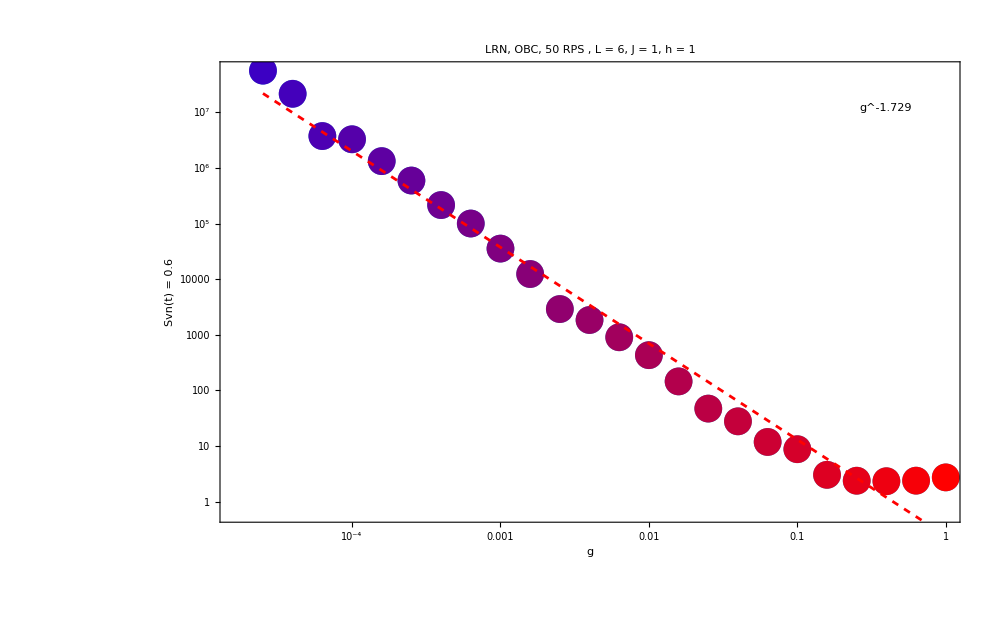

```mathematica
(*color function you defined*)
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
(*colors for each (h,t_hit) pair*)
colors=cf/@Rescale[Log10[pairsSorted[[All,1]]],{-6,0}];
(*wrap each point with its color*)
coloredPairs=MapThread[Style,{pairsSorted,colors}];
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[coloredPairs,PlotStyle->PointSize[.02],(*size of points*)ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
```

```mathematica
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw.png",powerlaw]
```

L_6_allLRNentropy_powerlaw.png

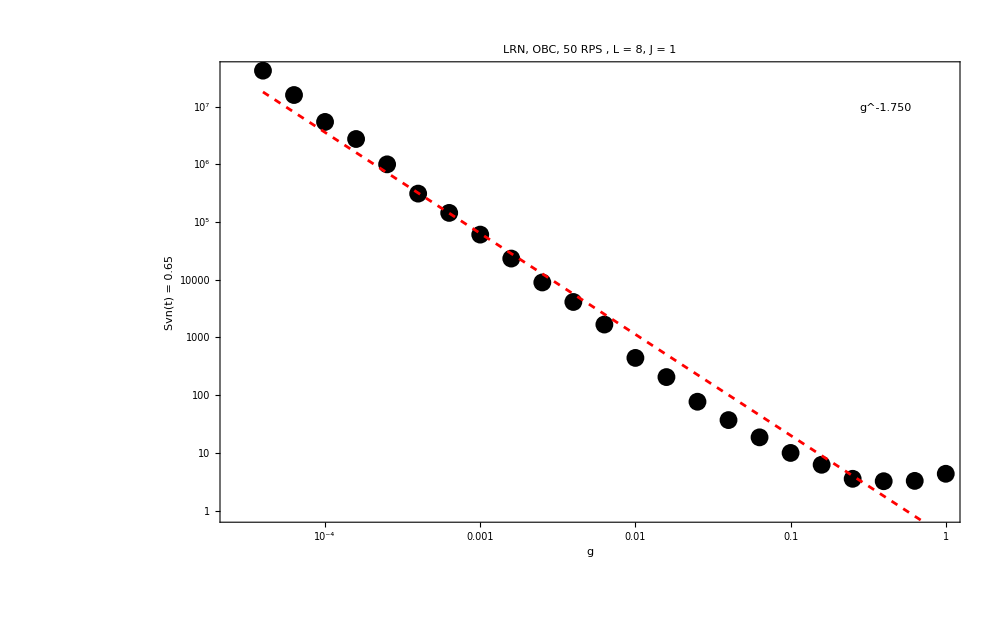

L_8_allLRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw.png",powerlaw]
```

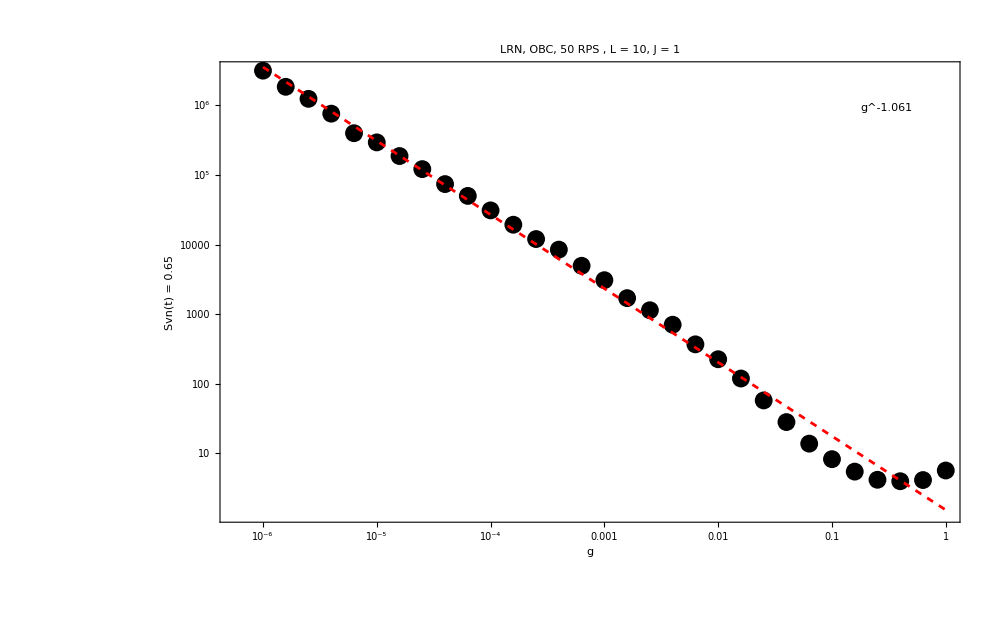

L_10_allLRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw.png",powerlaw]
```

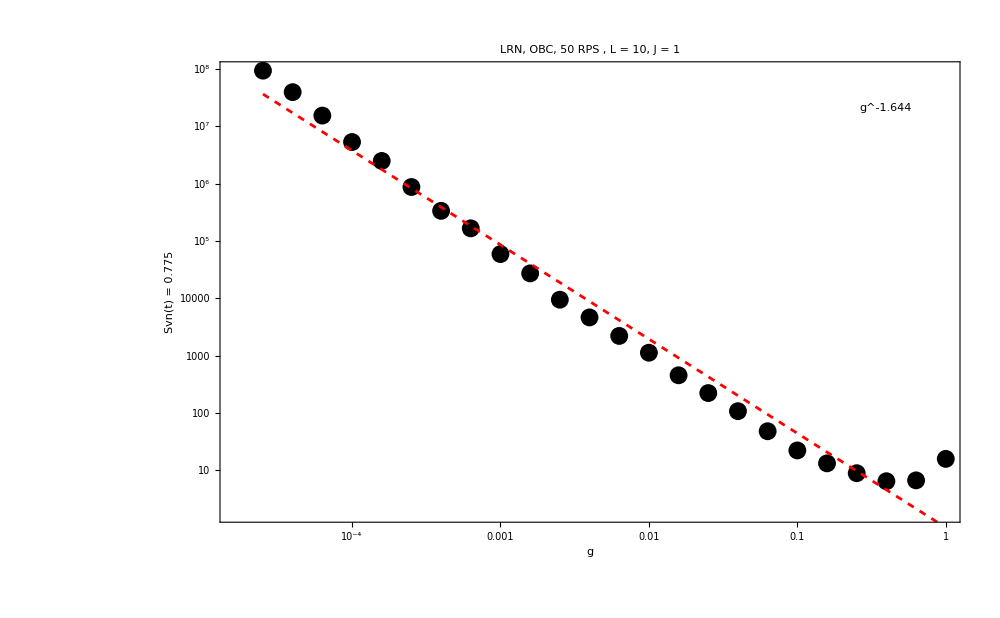

L_10_allLRNentropy_powerlaw2.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw2.png",powerlaw]
```

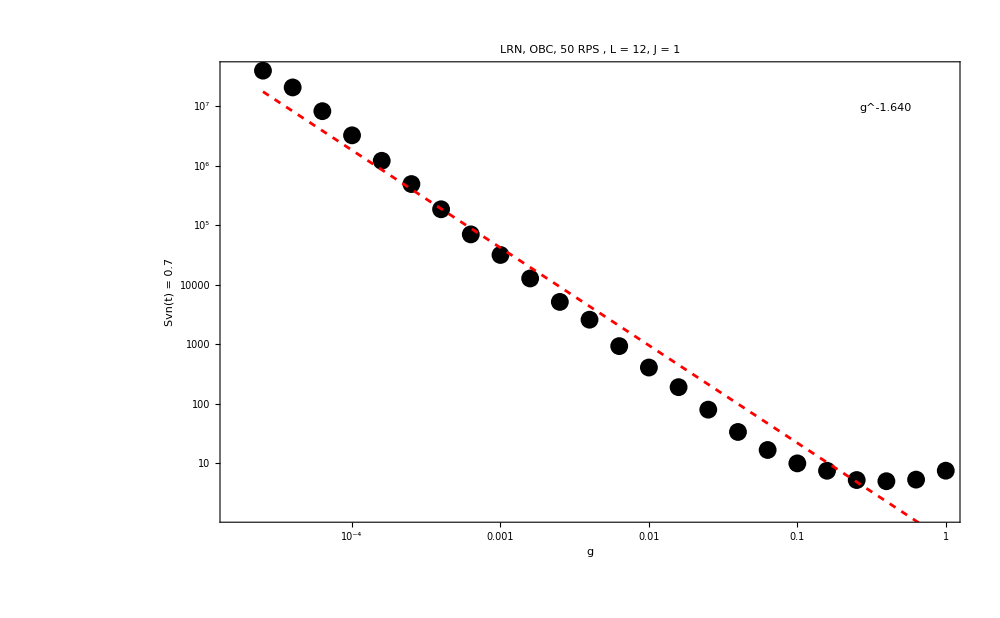

L_12_allLRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw.png",powerlaw]
```

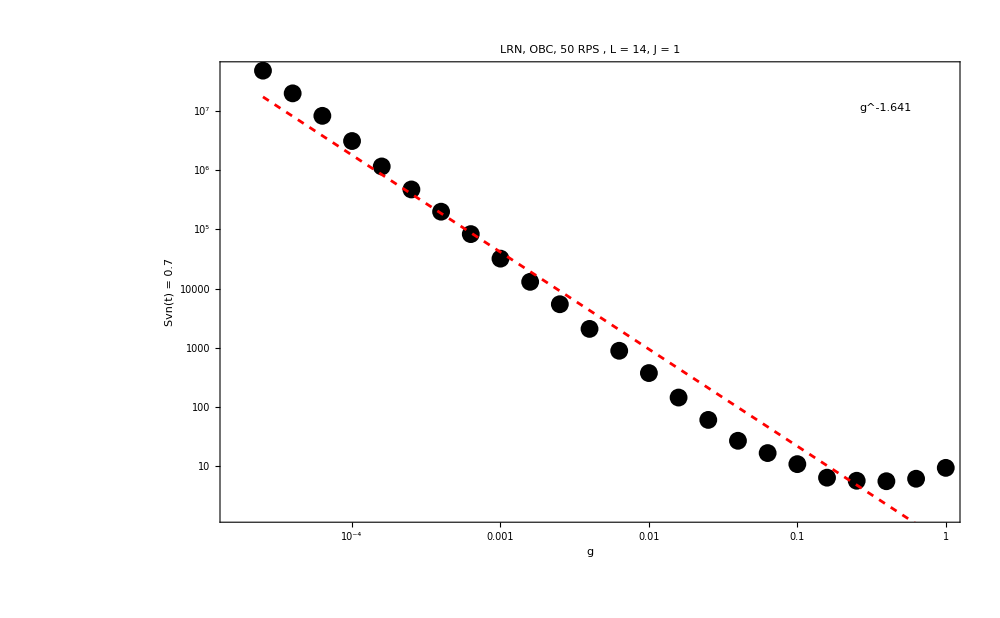

L_14_allLRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["g",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allLRNentropy_powerlaw.png",powerlaw]
```

## Example plot SRN

```mathematica
L=6;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\SRN_OBC_L_"<>ToString[L]<>"_50_RPS.m"];
```

```mathematica
limitzero=Mean[data[[1]]][[-1000;;-1]]//Mean;
limitone=Mean[data[[-1]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]/Log[2^(L/2)]];
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.75]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1",35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},GridLines->None,PlotRange->{All,{0,1}}],LogLinearPlot[{pageEntropy[L/2,L/2]/Log[2^(L/2)],limitzero,limitone},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed]},PlotRange->{All,{0,1}}]},Epilog->{Text[Style["h = 0",20,Blue,Bold],Scaled[{0.95,limitzero}],{36,1}],Text[Style["h = 1",20,Red,Bold],Scaled[{0.95,limitone}],{36,3}]
},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,{1,-1}}];
(*plot2=Show[plots,PlotRange->{All,{0,1}}]*)
```

```mathematica
Export["L_"<>ToString[L]<>"_SRNentropy.png",plot2]
```

L_14_SRNentropy.png

## Example plot all SRN

```mathematica
value=0.2;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.05]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},GridLines->None,PlotRange->{All,{0,1}}],LogLinearPlot[{pageEntropy[L/2,L/2]/Log[2^(L/2)],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]},PlotRange->{All,{0,1}}]},Epilog->{Text[Style["h = 0",20,Blue,Bold],Scaled[{0.95,limitzero}],{36,1}],Text[Style["h = 1",20,Red,Bold],Scaled[{0.95,limitone}],{36,3}]
},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
(*plot2=Show[plots,PlotRange->{All,{0,1}}]*)
```

```mathematica
(*cf expects input in[0,1];wrap it to accept x in[-6,0]*)
cfDomain=Function[x,cf[Rescale[x,{-6,0}]]];
bar=BarLegend[{cfDomain,{-6,0}},LegendLabel->Style["g = \!\(\*SuperscriptBox[\(10\), \(x\)]\)",20,Black],LabelStyle->{Black,18},LegendMarkerSize->{18,260}];
finalPlot=Legended[Show[plots,PlotRange->{All,{0,1}}],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_allSRNentropy.png",finalPlot]
```

L_6_allSRNentropy.png

## Power law

```mathematica
series=Table[Transpose[{tlist,Mean[data[[h]]]}],{h,Length[hlist]}];
Clear[hitTimesSampled];
Sstar=value;  (*threshold*)
pairs=DeleteMissing@MapThread[With[{pos=FirstPosition[#2[[All,2]],_?(#>=Sstar&),Missing["NoCrossing"]]},If[MissingQ[pos],Missing[],{#1,#2[[pos[[1]],1]]}]]&,{hlist,series}];
(*optional:sort by hit time*)
pairsSorted=SortBy[pairs,Last];
(*power-law:t≈a h^b*)
logData=Transpose[{Log[pairsSorted[[All,1]]],Log[pairsSorted[[All,2]]]}];
lm=LinearModelFit[logData,{1,z},z];
a=Exp[lm["BestFitParameters"][[1]]];
b=lm["BestFitParameters"][[2]];
rsq=lm["RSquared"];
  (*optional*)
{a,b,rsq}
```

{0.359438,-1.97806,0.998639}

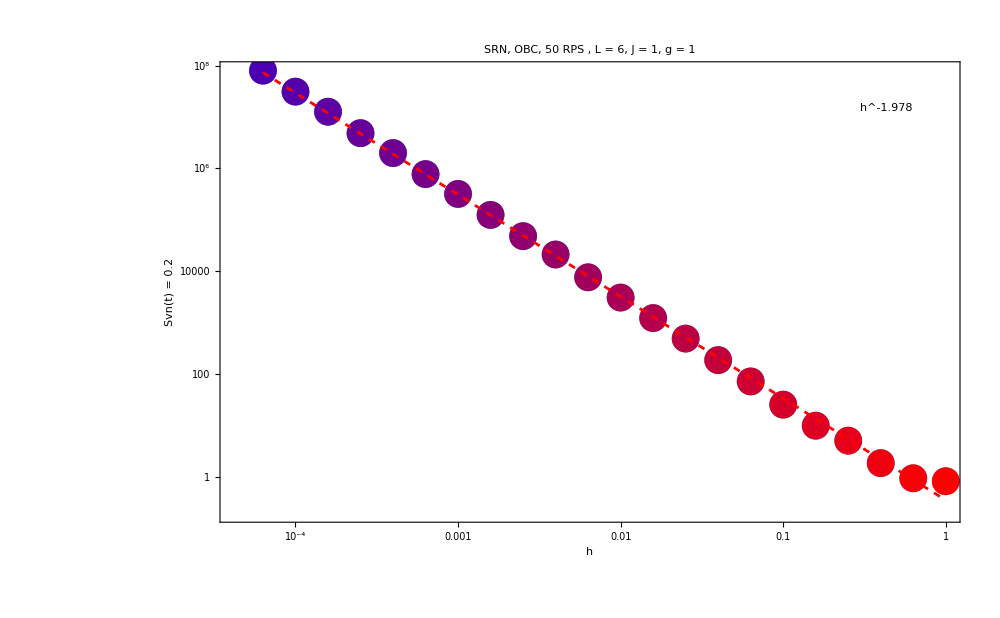

```mathematica
(*color function you defined*)
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
(*colors for each (h,t_hit) pair*)
colors=cf/@Rescale[Log10[pairsSorted[[All,1]]],{-6,0}];
(*wrap each point with its color*)
coloredPairs=MapThread[Style,{pairsSorted,colors}];
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[h,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[coloredPairs,PlotStyle->PointSize[.02],(*size of points*)ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1",35,Black],FrameLabel->{Style["h",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
```

```mathematica
Export["L_"<>ToString[L]<>"_allSRNentropy_powerlaw.png",powerlaw]
```

L_6_allSRNentropy_powerlaw.png

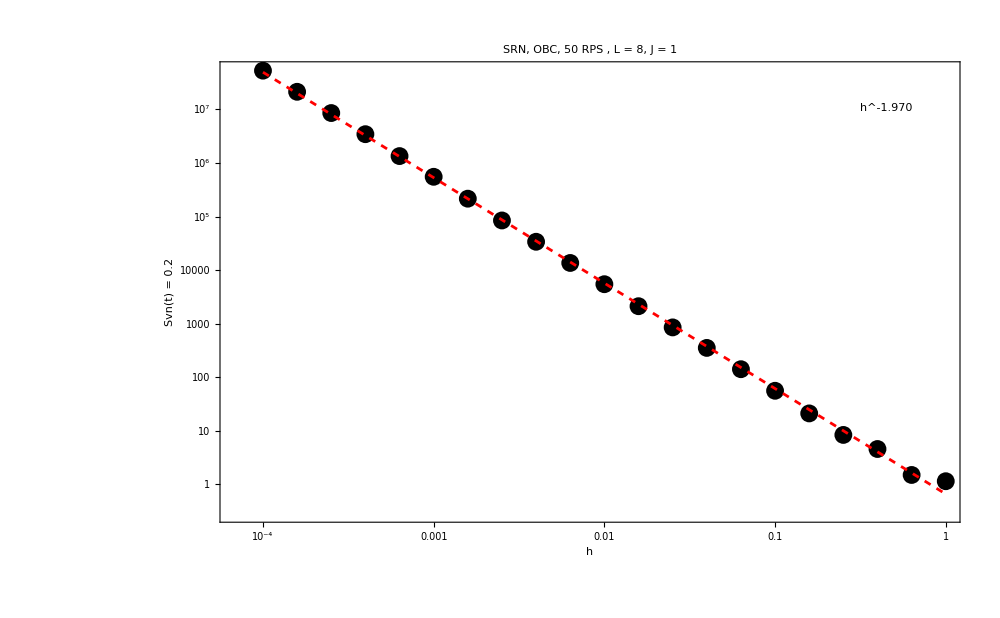

L_8_allSRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[h,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["h",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allSRNentropy_powerlaw.png",powerlaw]
```

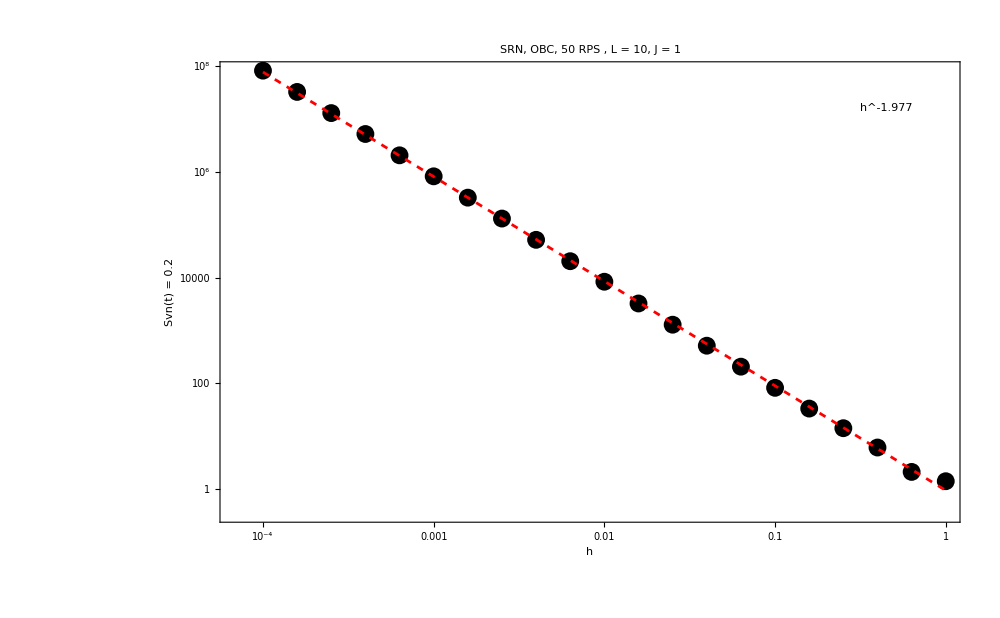

L_10_allSRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[h,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["h",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allSRNentropy_powerlaw.png",powerlaw]
```

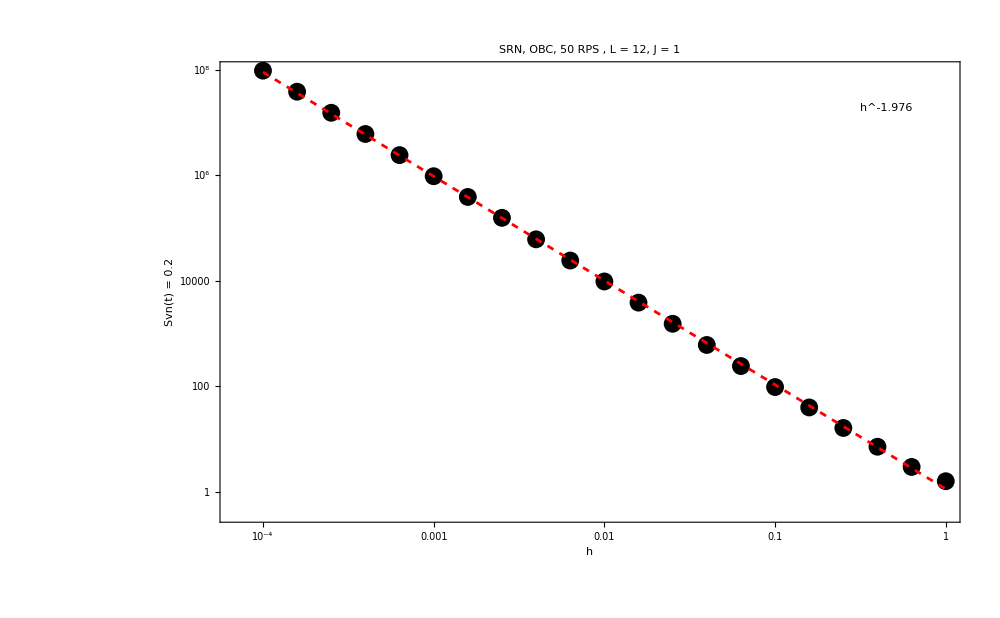

L_12_allSRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[h,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["h",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allSRNentropy_powerlaw.png",powerlaw]
```

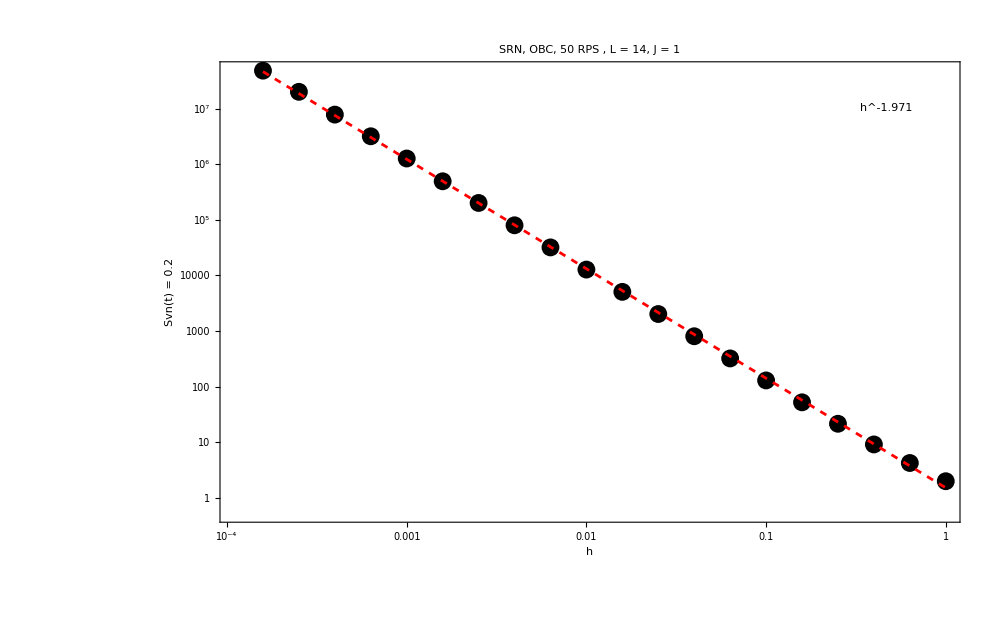

L_14_allSRNentropy_powerlaw.png

```mathematica
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.05],ImagePadding->3,ImageSize->70,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style[TraditionalForm@Superscript[h,NumberForm[b,{4,3}]],35,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->6];
xmin=Min[pairsSorted[[All,1]]];
xmax=Max[pairsSorted[[All,1]]];
powerlaw=Show[ListLogLogPlot[pairsSorted,ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, 50 RPS , L = "<>ToString[L]<>", J = "<>ToString[J],35,Black],FrameLabel->{Style["h",25,Black],Style["Svn(t) = "<>ToString[value],25,Black]},GridLines->None,PlotRange->All,PlotStyle->Black],LogLogPlot[a x^b,{x,xmin,xmax},PlotStyle->Directive[Red,Dashed]],Epilog->Inset[powLbl,Scaled[{0.90,0.90}]]]
Export["L_"<>ToString[L]<>"_allSRNentropy_powerlaw.png",powerlaw]
```